```mathematica
<<TopoTB`
```

#### Band

```mathematica
?VASPBand
```

```mathematica
path=SetDirectory[FileNameTake[NotebookFileName[],{1,-2}]];
poscar=Import["POSCAR","Table"];
kpoints=Import["KPOINTS","Table"];
eigenval=Import["EIGENVAL","Table"];
efermi=-2.0737;
```

```mathematica
(*ISPIN=1,SOC=2*)
ds=VASPBand[poscar,kpoints,eigenval,efermi,1,2,"Band.dat"]
```

Dataset[<>]

```mathematica
?BandLabelsPlot
```

{{0.,Γ},{1.1169,K},{1.67535,M},{2.2338,-K},{3.35071,Γ}}

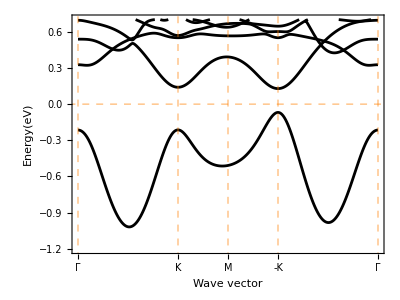

```mathematica
KK=Normal[ds[5]];
KK=KK/.{KK[[4,2]]->"-K"}
tband=Normal[ds[7]];
BandPlot[tband,KK,Black,0.005,3/4,{-1.2,0.7}]
```

```mathematica
BandLabelsPlot[tband,KK,Automatic,0.005,5/4,{-1.2,0.7}]
```

-Graphics-

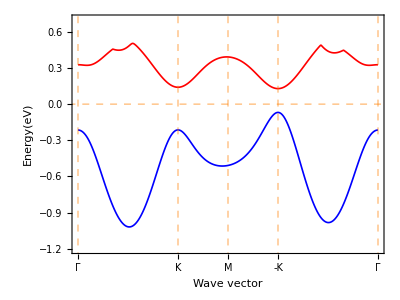

```mathematica
BandIndexPlot[{tband[[11]],tband[[12]]},KK,{Blue,Red},0.003,3/4,{-1.2,0.7}]
```

#### PBand

```mathematica
?VASPPBand
```

```mathematica
path=SetDirectory[FileNameTake[NotebookFileName[],{1,-2}]];
poscar=Import["POSCAR","Table"];
kpoints=Import["KPOINTS","Table"];
procar=Import["PROCAR","Table"];
efermi=-2.0737;
```

```mathematica
(*ISPIN=1, UpOrDown=1 (any value is acceptable when ISPIN=1), SOC=2*)
ds=VASPPBand[poscar,kpoints,procar,efermi,1,1,{2,0},{0},"PBand.dat"]
```

Dataset[<>]

```mathematica
?PBandPlot
```

```mathematica
KK=Normal[ds[5]];
KK=KK/.{KK[[4,2]]->"-K"}
tpband=Normal[ds[7]];
Normal[ds[6]]
```

{{0.,Γ},{1.1169,K},{1.67535,M},{2.2338,-K},{3.35071,Γ}}

<|K-Path(1/Å)→{1},Energy(eV)→{2},s→{3},py→{4},pz→{5},px→{6},dxy→{7},dyz→{8},dz2→{9},dxz→{10},x2-y2→{11},fy3x2→{12},fxyz→{13},fyz2→{14},fz3→{15},fxz2→{16},fzx2→{17},fx3→{18},tot→{19}|>

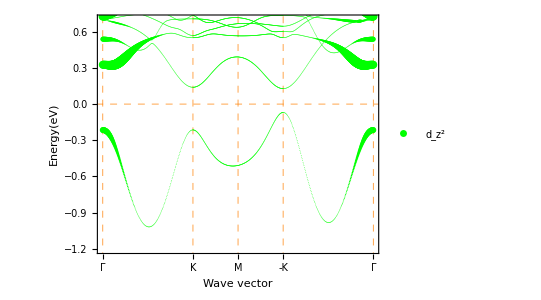

```mathematica
(*dz2 orbitals corresponds to 9 columns*)
fig1=PBandPlot[tpband,KK,{9},Green,"d_(z^2)",20,3/4,{-1.2,0.7}]
```

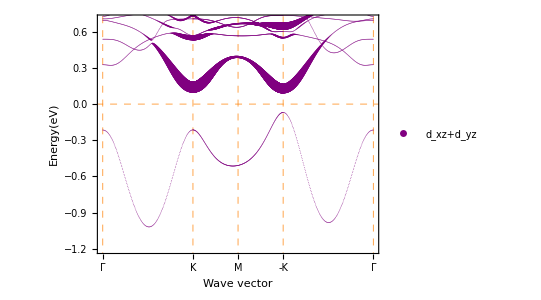

```mathematica
(*dxz+dyz orbitals correspond to columns 8 and 10*)
fig2=PBandPlot[tpband,KK,{8,10},Purple,"d_xz+d_yz",20,3/4,{-1.2,0.7}]
```

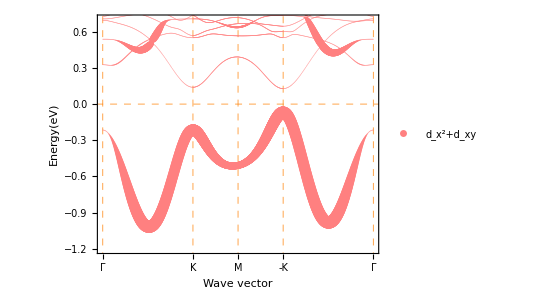

```mathematica
(*dx2-y2+dxy orbitals correspond to columns 7 and 11*)
fig3=PBandPlot[tpband,KK,{7,11},Pink,"d_(x^2)+d_xy",20,3/4,{-1.2,0.7}]
```

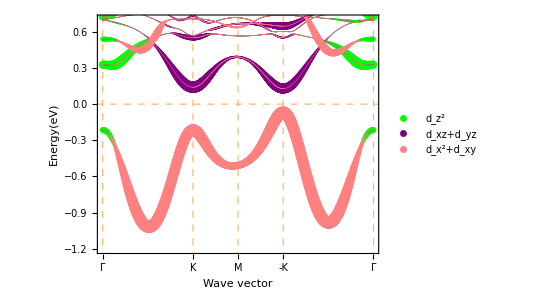

```mathematica
Show[fig1,fig2,fig3]
```

#### PBand-Sz

```mathematica
?VASPPBand
```

```mathematica
path=SetDirectory[FileNameTake[NotebookFileName[],{1,-2}]];
poscar=Import["POSCAR","Table"];
kpoints=Import["KPOINTS","Table"];
procar=Import["PROCAR","Table"];
efermi=-2.0737;
```

```mathematica
(*ISPIN=1, UpOrDown=1 (any value is acceptable when ISPIN=1), SOC=2*)
(*Sz Spin Component*)
ds=VASPPBand[poscar,kpoints,procar,efermi,1,1,{2,3},{0},"PBand-Sz.dat"]
```

Dataset[<>]

```mathematica
?PBandSpinPlot
```

```mathematica
KK=Normal[ds[5]];
KK=KK/.{KK[[4,2]]->"-K"}
tpband=Normal[ds[7]];
Normal[ds[6]]
```

{{0.,Γ},{1.1169,K},{1.67535,M},{2.2338,-K},{3.35071,Γ}}

<|K-Path(1/Å)→{1},Energy(eV)→{2},s→{3},py→{4},pz→{5},px→{6},dxy→{7},dyz→{8},dz2→{9},dxz→{10},x2-y2→{11},fy3x2→{12},fxyz→{13},fyz2→{14},fz3→{15},fxz2→{16},fzx2→{17},fx3→{18},tot→{19}|>

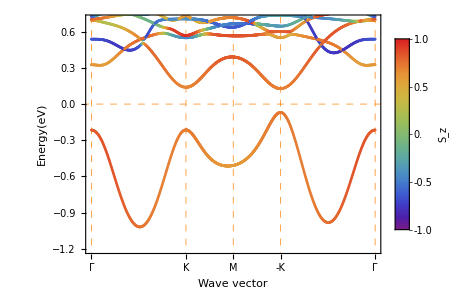

```mathematica
(*tot orbitals corresponds to 19 columns*)
(*Sz Spin Component*)
fig=PBandSpinPlot[tpband,KK,{19},"S_z",3/4,{-1.2,0.7}]
```